```mathematica
Quit[]
```

```mathematica
NotebookDirectory[];
SetDirectory[NotebookDirectory[]];
```

## Preliminaries

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NotebookDirectory[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
$Assumptions={Re[s]>4 m^2,m ∈ Reals};
```

```mathematica
ϵ := 10^-8;
iϵ:=I ϵ
```

```mathematica
jpacBlue=RGBColor[31/256,119/256,180/256];
jpacRed=RGBColor[214/256,39/256,40/256];
jpacGreen=RGBColor[0/256,158/256,115/256];
jpacGray = RGBColor[50/256,50/256,50/256];
jpacThick := Thickness[0.007];
```

```mathematica
sthRectangle[sL_,sR_]:={LightGray,Rectangle[{sL,-999},{sR,999}]}
sthColor[color_,sL_,sR_]:={color,Rectangle[{sL,-999},{sR,999}]}
vert[x_]:=Line[{{x,-999},{x,999}}]
frameLabel[label_]:=Style[label,Directive[jpacGray,Bold,12]]
frameLabel[label_,variable_]:=frameLabel[label<> ToString[variable]]
frameLabel[label_,variable_,units_]:=frameLabel[label<> ToString[variable]<>units]
```

```mathematica
jpacOptions:={PlotRange->{Automatic,Automatic},
Frame->True,
FrameTicksStyle->Directive[jpacGray,Bold,12],
ImageSize->Medium,
AspectRatio->1,
PlotStyle->{{jpacBlue, jpacThick},{jpacRed, jpacThick},{jpacGreen, jpacThick},{jpacGreen, jpacThick}},
FrameLabel->{{None ,None},{frameLabel["s [GeV^2]"],None}}}
```

## ρ Trajectory

### Parameters and definitions

```mathematica
q[s_]=√((s-4 m^2)/4);
ρ[s_]=2 q[s]/(√s);
q2hat[s_]=q[s]^2/Λ^2;
```

```mathematica
redat=Import["repart.dat","Table"];
rePartlow=Interpolation[redat];
m=√(redat[[1]][[1]])/2;
Λ=√2;
α0=0.491;
gρ=4.26308414;
γ=1.07360991;
cρ=3.47484722;
```

```mathematica
rePart[s_]=Which[Re[s]<4 m^2,0,Re[s]>=4 m^2&&Re[s]<=200, rePartlow[s],Re[s]>200 ,rePartlow[200] √(s/200)];
Imα[s_]=Which[Re[s]<=4 m^2,0,Re[s]> 4 m^2&& Re[s]<200,γ/π Log[1+π/γ ρ[s](gρ/3 q2hat[s]+cρ q2hat[s]^(1+rePart[s]))], Re[s]>=200,γ/π(rePart[s]Log[ q2hat[s]]+Log[π/γ ρ[s]cρ])];
```

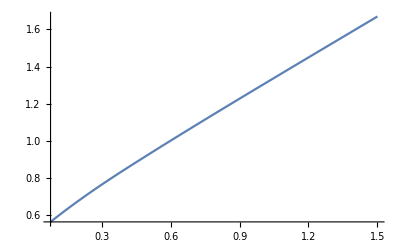

```mathematica
Plot[rePart[s],{s,4 m^2,1.5}]
```

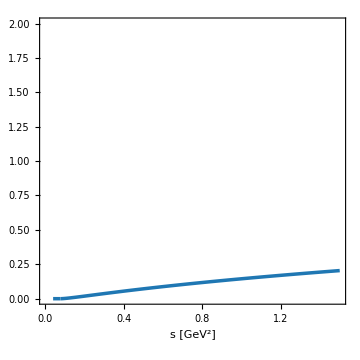

```mathematica
Plot[Imα[s],{s,2 m^2,1.5},PlotRange->{0,2},Evaluate[jpacOptions]]
```

### On the first sheet

Define the dispersion integral without an iϵ prescription, remember to put it in by hand in the argument!

```mathematica
dispIntI[s_]:=s/π Quiet@NIntegrate[(Imα[x]-Imα[s])/(x(x-s-iϵ)),{x,4 m^2,∞},Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20]-Imα[s]/π Log[1-(s+iϵ)/(4 m^2)]
αI[s_]:=α0 + dispIntI[s]
```

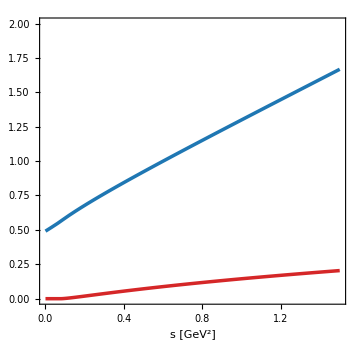

```mathematica
Plot[{αI[s]//Re, αI[s] //Im},{s,0,1.5}, PlotRange->{0,2}, Evaluate[jpacOptions]]
```

Plot the resulting partial wave amplitude

### On the unphysical sheet

The second sheet is stitched to the first by the discontinuity

```mathematica
(* ------------------------------------------------- *)
dispIntII[s_]:=s/π Quiet@NIntegrate[(Imα[x]-Imα[s])/(x(x-s+iϵ)),{x,4 m^2,∞},Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20]-Imα[s]/π Log[1-(s-iϵ)/(4 m^2)]
αII[s_]:=α0+dispIntII[s] +2I Imα[s]
f1[s_]:=gρ/3 q2hat[s]/(1-αII[s])
(* ------------------------------------------------- *)
```

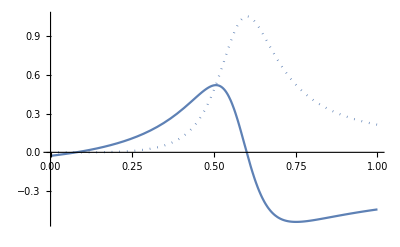

```mathematica
ReImPlot[f1[s],{s,0,1}]
```

```mathematica
PoleSearch[f_,xran_,yran_]:= NMinimize[{Abs[f[x+I y]]^-1, x>xran[[1]]&& x<xran[[2]]&& y>yran[[1]]&& y<yran[[2]]},{x,y},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->50,Method->"SimulatedAnnealing"]
```

```mathematica
ResParams[f_,sp_?NumericQ]:=
Module[{gi,g},
Print["√s_p = (", √sp*10^3, ") MeV"];
Print["M = ", Re[√sp]*10^3, " MeV"];
Print["Γ = ", -2Im[√sp]*10^3, " MeV"];
gi={};
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp)3/(2q[s])^2,s->sp,WorkingPrecision->50, Direction->1,Method->"SequenceLimit"]];
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp)3/(2q[s])^2,s->sp,WorkingPrecision->50,Direction->-1,Method->"SequenceLimit"]];
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp)3/(2q[s])^2,s->sp,WorkingPrecision->50, Direction->-I,Method->"SequenceLimit"]];
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp)3/(2q[s])^2,s->sp,WorkingPrecision->50, Direction->I,Method->"SequenceLimit"]];

g=Mean[gi];
Print["g's = ", Transpose[gi]//MatrixForm];
Print["|g_avg| = ", Abs[g]];
Print["arg(g_avg) = ", Arg[g] 180/π];
]
```

#### Continued Fractions definitions

```mathematica
generateCoeffs[svals_,f_]:=Module[{N,i,current,next, last, as,fvals},
(* Set up vector of f(s) *)
N=Length[svals];
fvals={};
Do[AppendTo[fvals,f[svals[[i]]]],{i,1,Length[svals]}];
(* empty list to output resulting coeffs *)
as={};
(* first coefficient *)
AppendTo[as,1./(svals[[2]]-svals[[1]])(fvals[[1]]/fvals[[2]]-1)];
(* loop over i = 2 to N-1 coefficients *)
Do[
last = 0; current = 0;
last= (as[[1]](svals[[l+1]]-svals[[1]]))/(1.-fvals[[1]]/fvals[[l+1]]);
current = last;
Do[
current = (as[[j]](svals[[l+1]]-svals[[j]]))/(1.+last);
last = current;
,{j,2,l-1}];
AppendTo[as, (1+current)/(svals[[l]]-svals[[l+1]])];
,{l,2,N-1}];
(* return list *)
as
]
generateCF[N_,srange_,f_,s_]:=
Module[{svals,as,fraction,current},
svals=Range[srange[[1]],srange[[2]],(srange[[2]]-srange[[1]])/N];
as = generateCoeffs[svals,f];
fraction =  as[[N]]*(s-svals[[N]]);
Do[
current = (as[[N-j]](s-svals[[N-j]]))/(1+fraction);
fraction = current;
,{j,1,N-1}];
f[svals[[1]]]/(1+fraction)
]
ContFrac[N_,srange_,f_]:=generateCF[N,srange,f,s];
```

#### Poles with CFs

```mathematica
(* Start with N = 50 *)
```

```mathematica
fCF[s_]=ContFrac[50,{0.1,1.0},f1];
Plot3D[Abs[fCF[x+I y]],{x,4 m^2,1.0},{y,-0.4,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large,MaxRecursion->10]
pole=PoleSearch[fCF,{4 m^2+ϵ,1.0},{-0.3,-ϵ}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{9.00974×10^-10,{x→0.57626,y→-0.110551}}

√s_p = (762.571-72.486 ⅈ) MeV

M = 762.571 MeV

Γ = 144.972 MeV

g's = (5.84426-0.651681 ⅈ
5.84426-0.651674 ⅈ
5.84426-0.651677 ⅈ
5.84425-0.651679 ⅈ)

|g_avg| = 5.88048

arg(g_avg) = -6.36262

```mathematica
(* Increase to N = 500 *)
```

```mathematica
fCF[s_]=ContFrac[500,{0.1,1.0},f1];
Plot3D[Abs[fCF[x+I y]],{x,4 m^2,1.0},{y,-0.4,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large,MaxRecursion->10]
pole=PoleSearch[fCF,{4 m^2+ϵ,1.0},{-0.3,-ϵ}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{4.63694×10^-10,{x→0.576263,y→-0.110553}}

√s_p = (762.573-72.4866 ⅈ) MeV

M = 762.573 MeV

Γ = 144.973 MeV

g's = (5.84431-0.651361 ⅈ
5.84431-0.651356 ⅈ
5.84431-0.651358 ⅈ
5.84431-0.651359 ⅈ)

|g_avg| = 5.8805

arg(g_avg) = -6.35947

#### Excited ρ’s

```mathematica
fprime[s_]:=1/(2-αII[s])
fCF[s_]=ContFrac[50,{0.1,3.0},fprime];
Plot3D[Abs[fCF[x+I y]],{x,4 m^2,4.0},{y,-0.9,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large,MaxRecursion->10]
pole=PoleSearch[fCF,{4 m^2+ϵ,3.0},{-0.9,-ϵ}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{5.22842×10^-12,{x→1.90966,y→-0.33717}}

√s_p = (1387.24-121.526 ⅈ) MeV

M = 1387.24 MeV

Γ = 243.052 MeV

g's = (10.5111+0.289904 ⅈ
10.5111+0.289905 ⅈ
10.5111+0.289904 ⅈ
10.5111+0.289904 ⅈ)

|g_avg| = 10.5151

arg(g_avg) = 1.57987

```mathematica
fCF[s_]=ContFrac[500,{0.1,3.0},fprime];
pole=PoleSearch[fCF,{4 m^2+ϵ,3.0},{-0.9,-ϵ}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

{5.31046×10^-12,{x→1.90966,y→-0.337174}}

√s_p = (1387.24-121.527 ⅈ) MeV

M = 1387.24 MeV

Γ = 243.055 MeV

g's = (10.5112+0.28994 ⅈ
10.5112+0.289941 ⅈ
10.5112+0.289941 ⅈ
10.5112+0.289941 ⅈ)

|g_avg| = 10.5152

arg(g_avg) = 1.58005

```mathematica
f3[s_]:=1/(3-αII[s])
fCF[s_]=ContFrac[50,{0.1,4.0},f3];
Plot3D[Abs[fCF[x+I y]],{x,4 m^2,4.0},{y,-0.9,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large,MaxRecursion->10]
pole=PoleSearch[fCF,{4 m^2+ϵ,4.0},{-0.9,-ϵ}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{4.10686×10^-10,{x→3.24517,y→-0.474559}}

√s_p = (1806.22-131.368 ⅈ) MeV

M = 1806.22 MeV

Γ = 262.736 MeV

g's = (7.85742+0.25758 ⅈ
7.85747+0.257576 ⅈ
7.85745+0.257552 ⅈ
7.85745+0.257604 ⅈ)

|g_avg| = 7.86167

arg(g_avg) = 1.87756

```mathematica
fCF[s_]=ContFrac[500,{0.1,4.0},f3];
pole=PoleSearch[fCF,{4 m^2+ϵ,4.0},{-0.9,-ϵ}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

{1.61191×10^-12,{x→3.24517,y→-0.47456}}

√s_p = (1806.22-131.368 ⅈ) MeV

M = 1806.22 MeV

Γ = 262.737 MeV

g's = (7.85747+0.257626 ⅈ
7.85747+0.257626 ⅈ
7.85747+0.257626 ⅈ
7.85747+0.257626 ⅈ)

|g_avg| = 7.86169

arg(g_avg) = 1.87791